```mathematica
Functions
```

Functions

```mathematica
PDeath[day_,accept_,endp_]:=Module[{a,b,p},
a=accept[[;;,day,2]]/Total[accept[[;;,day,2]]];
(*Probability that outbreak has died out*)
b=endp[[;;,day,2]];
p=Total[a*b];
Return[p];
];

(*Note: Mean sizes may be inaccurate if sizes are calculated with a cap*)
FindMeanSize[s_,val_]:=Module[{ss,m},
ss=s[[val]];
m=Total[Table[ss[[i,1]]*ss[[i,2]],{i,1,Length[ss]}]];
Return[m];
];

FindMedianSize[s_,val_]:=Module[{ss,cs,med},
ss=s[[val]];
cs=ss;
For[i=2,i<=Length[ss],i++,
cs[[i,2]]=cs[[i,2]]+cs[[i-1,2]];
];
med=Select[cs,#[[2]]>=0.5&][[1,1]];
Return[med];
];

fourParamChartStyle={RGBColor["#4477AA"],RGBColor["#117733"],RGBColor["#DDCC77"],RGBColor["#CC6677"]};
```

```mathematica
Import Data
```

Data Import

```mathematica
FileNames[]
```

{0.04,0.06,0.08,0.1}

```mathematica
SetDirectory["/Users/johnfozard/OINK/output_variable_detection_delay"];
p=0.04;
times=Flatten[Import["/Users/johnfozard/OINK/Data/Time_points.dat","Table"]];
accept4=Table[Import[ToString[p]<>"/Acceptance_rate"<>ToString[i]<>".dat"],{i,1,40}];
sizedist4=Table[Import[ToString[p]<>"/Sizes_time_"<>ToString[times[[i]]]<>".dat","Table"],{i,1,Length[times]}];
origdist4=Table[Import[ToString[p]<>"/Origin_stats_"<>ToString[times[[i]]]<>".dat","Table"],{i,1,Length[times]}];
For[i=1,i<=Length[origdist4],i++,
origdist4[[i,;;,1]]=-origdist4[[i,;;,1]];
];
pend4=Import[ToString[p]<>"/P_Outbreak_End.dat","Table"];

p=0.06;
accept6=Table[Import[ToString[p]<>"/Acceptance_rate"<>ToString[i]<>".dat"],{i,1,40}];
sizedist6=Table[Import[ToString[p]<>"/Sizes_time_"<>ToString[times[[i]]]<>".dat","Table"],{i,1,Length[times]}];
origdist6=Table[Import[ToString[p]<>"/Origin_stats_"<>ToString[times[[i]]]<>".dat","Table"],{i,1,Length[times]}];
For[i=1,i<=Length[origdist6],i++,
origdist6[[i,;;,1]]=-origdist6[[i,;;,1]];
];
pend6=Import[ToString[p]<>"/P_Outbreak_End.dat","Table"];

p=0.08;
accept8=Table[Import[ToString[p]<>"/Acceptance_rate"<>ToString[i]<>".dat"],{i,1,40}];
sizedist8=Table[Import[ToString[p]<>"/Sizes_time_"<>ToString[times[[i]]]<>".dat","Table"],{i,1,Length[times]}];
origdist8=Table[Import[ToString[p]<>"/Origin_stats_"<>ToString[times[[i]]]<>".dat","Table"],{i,1,Length[times]}];
For[i=1,i<=Length[origdist8],i++,
origdist8[[i,;;,1]]=-origdist8[[i,;;,1]];
];
pend8=Import[ToString[p]<>"/P_Outbreak_End.dat","Table"];

p=0.1;
accept10=Table[Import[ToString[p]<>"/Acceptance_rate"<>ToString[i]<>".dat"],{i,1,40}];
sizedist10=Table[Import[ToString[p]<>"/Sizes_time_"<>ToString[times[[i]]]<>".dat","Table"],{i,1,Length[times]}];
origdist10=Table[Import[ToString[p]<>"/Origin_stats_"<>ToString[times[[i]]]<>".dat","Table"],{i,1,Length[times]}];
For[i=1,i<=Length[origdist10],i++,
origdist10[[i,;;,1]]=-origdist10[[i,;;,1]];
];
pend10=Import[ToString[p]<>"/P_Outbreak_End.dat","Table"];
```

```mathematica
Figure 1A
```

A Figure

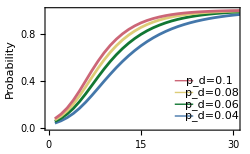

```mathematica
Show[ListLinePlot[{pend4,pend6,pend8,pend10},PlotRange->{{0,30.5},All},Frame->True,PlotStyle->fourParamChartStyle,FrameLabel->{{"Probability",None},{"Days after initial detection","Estimated probability outbreak has ended"}},FrameStyle->Directive[Black,FontSize->10],ImageSize->250],Graphics[{fourParamChartStyle[[4]],Line[{{20.5,0.4},{23.5,0.4}}]}],Graphics[{fourParamChartStyle[[3]],Line[{{20.5,0.3},{23.5,0.3}}]}],Graphics[{fourParamChartStyle[[2]],Line[{{20.5,0.2},{23.5,0.2}}]}],Graphics[{fourParamChartStyle[[1]],Line[{{20.5,0.1},{23.5,0.1}}]}],Graphics[Text["p_d=0.1",{26.2,0.4}]],Graphics[Text["p_d=0.08",{26.5,0.3}]],Graphics[Text["p_d=0.06",{26.5,0.2}]],Graphics[Text["p_d=0.04",{26.5,0.1}]]]
```

```mathematica
Population size conditional on not dying out at day 14
```

14 at conditional day dying not on out Population size

90

71

60

54

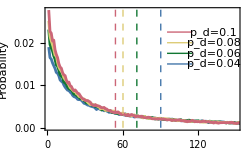

```mathematica
val=14;
s4=sizedist4[[val]];
s6=sizedist6[[val]];
s8=sizedist8[[val]];
s10=sizedist10[[val]];
y1=0.2;
y2=0.24;
y3=0.28;
y4=0.32;
cs4=s4;
For[i=2,i<=Length[s4],i++,
cs4[[i,2]]=cs4[[i,2]]+cs4[[i-1,2]];
];
cs6=s6;
For[i=2,i<=Length[s6],i++,
cs6[[i,2]]=cs6[[i,2]]+cs6[[i-1,2]];
];
cs8=s8;
For[i=2,i<=Length[s8],i++,
cs8[[i,2]]=cs8[[i,2]]+cs8[[i-1,2]];
];
cs10=s10;
For[i=2,i<=Length[s10],i++,
cs10[[i,2]]=cs10[[i,2]]+cs10[[i-1,2]];
];
Med[s_]:= Median[WeightedData[Map[First,s], Map[Last, s]]];

med4 = Med[s4]
med6 = Med[s6]
med8 = Med[s8]
med10 = Med[s10]
y1=0.015;
dy=0.0025;
y2=y1+dy;
y3=y2+dy;
y4=y3+dy;
x1 = 95;
x2 = x1+20;
p1=Show[ListLinePlot[{s4[[2;;]],s6[[2;;]],s8[[2;;]],s10[[2;;]]},PlotRange->{{1,150},All},Frame->True,PlotStyle->fourParamChartStyle,FrameLabel->{{"Probability",None},{"Number of infected individuals","Day 14"}},FrameStyle->Directive[Black,FontSize->10],ImageSize->250],Graphics[{fourParamChartStyle[[4]],Line[{{x1,y4},{x2,y4}}]}],Graphics[{fourParamChartStyle[[3]],Line[{{x1,y3},{x2,y3}}]}],Graphics[{fourParamChartStyle[[2]],Line[{{x1,y2},{x2,y2}}]}],Graphics[{fourParamChartStyle[[1]],Line[{{x1,y1},{x2,y1}}]}],Graphics[Text["p_d=0.1",{132,y4}]],Graphics[Text["p_d=0.08",{132,y3}]],Graphics[Text["p_d=0.06",{132,y2}]],Graphics[Text["p_d=0.04",{132,y1}]],Graphics[{Dashed,fourParamChartStyle[[1]],Line[{{med4,0},{med4,0.5}}]}],Graphics[{Dashed,fourParamChartStyle[[2]],Line[{{med6,0},{med6,0.5}}]}],Graphics[{Dashed,fourParamChartStyle[[3]],Line[{{med8,0},{med8,0.5}}]}],Graphics[{Dashed,fourParamChartStyle[[4]],Line[{{med10,0},{med10,0.5}}]}]]
```

```mathematica
Median outbreak sizes
```

Median outbreak sizes

```mathematica
{med4,med6,med8,med10}
```

{90,71,60,54}

```mathematica
Time of spillover event
```

event of spillover Time

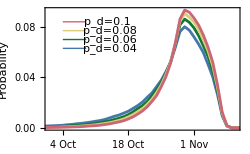

```mathematica
val=29;
y1=0.0628;
dy=0.007;
y2=y1+dy;
y3=y2+dy;
y4=y3+dy;
x1=-51;
dx=5;
x2=-41;
Show[ListLinePlot[{origdist4[[val]],origdist6[[val]],origdist8[[val]],origdist10[[val]]},PlotRange->{{-54,-14},All},Frame->True,Axes->False,PlotStyle->fourParamChartStyle,FrameLabel->{{"Probability",None},{"Date","Time of spillover event"}},FrameStyle->Directive[Black,FontSize->10],ImageSize->250,FrameTicks->{{Automatic,Automatic},{{{-23-28,"4 Oct"},{-23-21,"11 Oct"},{-23-14,"18 Oct"},{-23-7,"25 Oct"},{-23,"1 Nov"},{-23+7,"8 Nov"}},Automatic}}],Graphics[{fourParamChartStyle[[4]],Line[{{x1,y4},{x1+dx,y4}}]}],Graphics[{fourParamChartStyle[[3]],Line[{{x1,y3},{x1+dx,y3}}]}],Graphics[{fourParamChartStyle[[2]],Line[{{x1,y2},{x1+dx,y2}}]}],Graphics[{fourParamChartStyle[[1]],Line[{{x1,y1},{x1+dx,y1}}]}],Graphics[Text["p_d=0.1",{x2-0.5,y4}]],Graphics[Text["p_d=0.08",{x2,y3}]],Graphics[Text["p_d=0.06",{x2,y2}]],Graphics[Text["p_d=0.04",{x2,y1}]]]
```

```mathematica
Maximum likelihood times relative to first observation
```

{first likelihood Maximum observation relative to,2 first likelihood Maximum observation relative to,3 first likelihood Maximum observation relative to,4 first likelihood Maximum observation relative to,5 first likelihood Maximum observation relative to,6 first likelihood Maximum observation relative to,7 first likelihood Maximum observation relative to,8 first likelihood Maximum observation relative to,9 first likelihood Maximum observation relative to,10 first likelihood Maximum observation relative to,11 first likelihood Maximum observation relative to,12 first likelihood Maximum observation relative to,13 first likelihood Maximum observation relative to,14 first likelihood Maximum observation relative to,15 first likelihood Maximum observation relative to,16 first likelihood Maximum observation relative to,17 first likelihood Maximum observation relative to,18 first likelihood Maximum observation relative to,19 first likelihood Maximum observation relative to,20 first likelihood Maximum observation relative to,21 first likelihood Maximum observation relative to,22 first likelihood Maximum observation relative to,23 first likelihood Maximum observation relative to,24 first likelihood Maximum observation relative to,25 first likelihood Maximum observation relative to,26 first likelihood Maximum observation relative to,27 first likelihood Maximum observation relative to,28 first likelihood Maximum observation relative to,29 first likelihood Maximum observation relative to,30 first likelihood Maximum observation relative to,31 first likelihood Maximum observation relative to,32 first likelihood Maximum observation relative to,90 first likelihood Maximum observation relative to}

```mathematica
Sort[origdist4[[val]],#1[[2]]>#2[[2]]&][[1,1]]
Sort[origdist6[[val]],#1[[2]]>#2[[2]]&][[1,1]]
Sort[origdist8[[val]],#1[[2]]>#2[[2]]&][[1,1]]
Sort[origdist10[[val]],#1[[2]]>#2[[2]]&][[1,1]]
```

-25

-25

-25

«1 more identical outputs»

```mathematica
Mean times relative to first observation
```

{first Mean observation relative to,2 first Mean observation relative to,3 first Mean observation relative to,4 first Mean observation relative to,5 first Mean observation relative to,6 first Mean observation relative to,7 first Mean observation relative to,8 first Mean observation relative to,9 first Mean observation relative to,10 first Mean observation relative to,11 first Mean observation relative to,12 first Mean observation relative to,13 first Mean observation relative to,14 first Mean observation relative to,15 first Mean observation relative to,16 first Mean observation relative to,17 first Mean observation relative to,18 first Mean observation relative to,19 first Mean observation relative to,20 first Mean observation relative to,21 first Mean observation relative to,22 first Mean observation relative to,23 first Mean observation relative to,24 first Mean observation relative to,25 first Mean observation relative to,26 first Mean observation relative to,27 first Mean observation relative to,28 first Mean observation relative to,29 first Mean observation relative to,30 first Mean observation relative to,31 first Mean observation relative to,32 first Mean observation relative to,90 first Mean observation relative to}

```mathematica
Total[Table[origdist4[[val,i,1]]*origdist4[[val,i,2]],{i,1,Length[origdist4[[val]]]}]]
Total[Table[origdist6[[val,i,1]]*origdist6[[val,i,2]],{i,1,Length[origdist6[[val]]]}]]
Total[Table[origdist8[[val,i,1]]*origdist8[[val,i,2]],{i,1,Length[origdist8[[val]]]}]]
Total[Table[origdist10[[val,i,1]]*origdist10[[val,i,2]],{i,1,Length[origdist10[[val]]]}]]
```

-27.5047

-26.4193

-25.7579

-25.3107

```mathematica
Final distribution of R0
```

distribution Final of R0

{0.00576872,0.012659,0.0211485,0.0319417,0.0455494,0.0627857,0.0832269,0.10655,0.122472,0.121517,0.101686,0.0758827,0.0547,0.0389244,0.0280163,0.0204452,0.0152478,0.011387,0.00867684,0.00667916,0.00507204,0.00396633,0.00326437,0.00247269,0.00198976,0.00154642,0.0012469,0.00103974,0.000835225,0.00072175,0.000531746,0.000426189,0.000364174,0.000310075,0.000245421,0.000190004,0.000158336,0.000159656,0.000108197,0.000087085}

{{0.1,0.00576872},{0.2,0.0184277},{0.3,0.0395762},{0.4,0.0715179},{0.5,0.117067},{0.6,0.179853},{0.7,0.26308},{0.8,0.36963},{0.9,0.492102},{1.,0.613618},{1.1,0.715305},{1.2,0.791187},{1.3,0.845887},{1.4,0.884812},{1.5,0.912828},{1.6,0.933273},{1.7,0.948521},{1.8,0.959908},{1.9,0.968585},{2.,0.975264},{2.1,0.980336},{2.2,0.984302},{2.3,0.987567},{2.4,0.990039},{2.5,0.992029},{2.6,0.993576},{2.7,0.994822},{2.8,0.995862},{2.9,0.996697},{3.,0.997419},{3.1,0.997951},{3.2,0.998377},{3.3,0.998741},{3.4,0.999051},{3.5,0.999297},{3.6,0.999487},{3.7,0.999645},{3.8,0.999805},{3.9,0.999913},{4.,1.}}

{{0.1,0.00576872},{0.2,0.012659},{0.3,0.0211485},{0.4,0.0319417},{0.5,0.0455494},{0.6,0.0627857},{0.7,0.0832269},{0.8,0.10655},{0.9,0.122472},{1.,0.121517},{1.1,0.101686},{1.2,0.0758827},{1.3,0.0547},{1.4,0.0389244},{1.5,0.0280163},{1.6,0.0204452},{1.7,0.0152478},{1.8,0.011387},{1.9,0.00867684},{2.,0.00667916},{2.1,0.00507204},{2.2,0.00396633},{2.3,0.00326437},{2.4,0.00247269},{2.5,0.00198976},{2.6,0.00154642},{2.7,0.0012469},{2.8,0.00103974},{2.9,0.000835225},{3.,0.00072175},{3.1,0.000531746},{3.2,0.000426189},{3.3,0.000364174},{3.4,0.000310075},{3.5,0.000245421},{3.6,0.000190004},{3.7,0.000158336},{3.8,0.000159656},{3.9,0.000108197},{4.,0.000087085}}

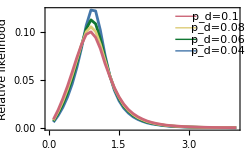

```mathematica
a4=accept4[[;;,-1,2]]/Total[accept4[[;;,-1,2]]]
ca4=a4;
For[i=2,i<=Length[ca4],i++,
ca4[[i]]=ca4[[i]]+ca4[[i-1]];
];
ca4=Partition[Riffle[Table[0.1*i,{i,1,40}],ca4],2]
a4=Partition[Riffle[Table[0.1*i,{i,1,40}],a4],2]

a6=accept6[[;;,-1,2]]/Total[accept6[[;;,-1,2]]];
ca6=a6;
For[i=2,i<=Length[ca6],i++,
ca6[[i]]=ca6[[i]]+ca6[[i-1]];
];
ca6=Partition[Riffle[Table[0.1*i,{i,1,40}],ca6],2];
a6=Partition[Riffle[Table[0.1*i,{i,1,40}],a6],2];

a8=accept8[[;;,-1,2]]/Total[accept8[[;;,-1,2]]];
ca8=a8;
For[i=2,i<=Length[ca8],i++,
ca8[[i]]=ca8[[i]]+ca8[[i-1]];
];
ca8=Partition[Riffle[Table[0.1*i,{i,1,40}],ca8],2];
a8=Partition[Riffle[Table[0.1*i,{i,1,40}],a8],2];

a10=accept10[[;;,-1,2]]/Total[accept10[[;;,-1,2]]];
ca10=a10;
For[i=2,i<=Length[ca10],i++,
ca10[[i]]=ca10[[i]]+ca10[[i-1]];
];
ca10=Partition[Riffle[Table[0.1*i,{i,1,40}],ca10],2];
a10=Partition[Riffle[Table[0.1*i,{i,1,40}],a10],2];

y1=0.08;
dy=0.012;
y2=y1+dy;
y3=y2+dy;
y4=y3+dy;
x1=2.7;
dx=0.45;
x2=3.6;
Show[ListLinePlot[{a4,a6,a8,a10},Frame->True,Axes->False,PlotStyle->fourParamChartStyle,FrameLabel->{"R_0","Relative likelihood"},FrameStyle->Directive[Black,FontSize->10],ImageSize->250],Graphics[{fourParamChartStyle[[4]],Line[{{x1,y4},{x1+dx,y4}}]}],Graphics[{fourParamChartStyle[[3]],Line[{{x1,y3},{x1+dx,y3}}]}],Graphics[{fourParamChartStyle[[2]],Line[{{x1,y2},{x1+dx,y2}}]}],Graphics[{fourParamChartStyle[[1]],Line[{{x1,y1},{x1+dx,y1}}]}],Graphics[Text["p_d=0.1",{x2-0.05,y4}]],Graphics[Text["p_d=0.08",{x2,y3}]],Graphics[Text["p_d=0.06",{x2,y2}]],Graphics[Text["p_d=0.04",{x2,y1}]]]
```

```mathematica
Statistics of R0: Maximum likelihood
```

of Statistics (R0:likelihood Maximum)

```mathematica
Sort[a4,#1[[2]]>#2[[2]]&][[1,1]]
Sort[a6,#1[[2]]>#2[[2]]&][[1,1]]
Sort[a8,#1[[2]]>#2[[2]]&][[1,1]]
Sort[a10,#1[[2]]>#2[[2]]&][[1,1]]
```

0.9

0.9

0.9

«1 more identical outputs»

```mathematica
Statistics of R0: 95 per cent confidence interval
```

of Statistics (R0:95 cent confidence interval per)

```mathematica
ca4
```

{{0.1,0.00576872},{0.2,0.0184277},{0.3,0.0395762},{0.4,0.0715179},{0.5,0.117067},{0.6,0.179853},{0.7,0.26308},{0.8,0.36963},{0.9,0.492102},{1.,0.613618},{1.1,0.715305},{1.2,0.791187},{1.3,0.845887},{1.4,0.884812},{1.5,0.912828},{1.6,0.933273},{1.7,0.948521},{1.8,0.959908},{1.9,0.968585},{2.,0.975264},{2.1,0.980336},{2.2,0.984302},{2.3,0.987567},{2.4,0.990039},{2.5,0.992029},{2.6,0.993576},{2.7,0.994822},{2.8,0.995862},{2.9,0.996697},{3.,0.997419},{3.1,0.997951},{3.2,0.998377},{3.3,0.998741},{3.4,0.999051},{3.5,0.999297},{3.6,0.999487},{3.7,0.999645},{3.8,0.999805},{3.9,0.999913},{4.,1.}}

```mathematica
{Select[ca4,#[[2]]<0.025&][[-1]],Select[ca4,#[[2]]>0.975&][[1]]}
{Select[ca6,#[[2]]<0.025&][[-1]],Select[ca6,#[[2]]>0.975&][[1]]}
{Select[ca8,#[[2]]<0.025&][[-1]],Select[ca8,#[[2]]>0.975&][[1]]}
{Select[ca10,#[[2]]<0.025&][[-1]],Select[ca10,#[[2]]>0.975&][[1]]}
```

{{0.2,0.0184277},{2.,0.975264}}

{{0.2,0.0218222},{2.1,0.976984}}

{{0.2,0.0246401},{2.2,0.979653}}

{{0.1,0.00873597},{2.2,0.977572}}